# OOP for operator couples

## Utilities

```mathematica
propagator[1/2CC sxx, sxy -syx, ξ/2] //basisProjectAlpha
```

1/4 CC (Sxx-Syy+(Sxx+Syy) Cos[ξ]+(Sza-Szb) Sin[ξ])

### Spin operators (product basis)

```mathematica
sx = {{0, 1}, {1, 0}}/2;
sy = {{0, -I}, {I, 0}}/2;
sz = {{1, 0}, {0, -1}}/2;
ee2x2 = {{1, 0}, {0, 1}};
zz2x2 = {{0, 0}, {0, 0}};
ee=1/2*TensorProduct[ee2x2, ee2x2]//ArrayFlatten;
sxa=TensorProduct[sx, ee2x2]//ArrayFlatten;
sya=TensorProduct[sy, ee2x2]//ArrayFlatten;
sza=TensorProduct[sz, ee2x2]//ArrayFlatten;
sxb=TensorProduct[ee2x2, sx]//ArrayFlatten;
syb=TensorProduct[ee2x2, sy]//ArrayFlatten;
szb=TensorProduct[ee2x2, sz]//ArrayFlatten;
sxx=2*TensorProduct[sx, sx]//ArrayFlatten;
sxy=2*TensorProduct[sx, sy]//ArrayFlatten;
sxz=2*TensorProduct[sx, sz]//ArrayFlatten;
syx=2*TensorProduct[sy, sx]//ArrayFlatten;
syy=2*TensorProduct[sy, sy]//ArrayFlatten;
syz=2*TensorProduct[sy, sz]//ArrayFlatten;
szx=2*TensorProduct[sz, sx]//ArrayFlatten;
szy=2*TensorProduct[sz, sy]//ArrayFlatten;
szz=2*TensorProduct[sz, sz]//ArrayFlatten;
zz = TensorProduct[zz2x2, zz2x2]//ArrayFlatten;
productBasis = {ee, sxa, sya, sza, sxb, syb, szb, sxx,sxy,sxz,syx,syy,syz, szx, szy, szz};
productBasisAlpha = {"II/2", "Sxa","Sya","Sza","Sxb","Syb","Szb","Sxx","Sxy","Sxz","Syx","Syy","Syz","Szx","Szy","Szz"};
```

### Functions

```mathematica
commutator[a_, b_] := a.b - b.a
propagator[a_, b_, ξ_] := TrigReduce[ExpToTrig[MatrixExp[-I*ξ*b].a.MatrixExp[I*ξ*b]]]

projectionScalarProd[a_, basis_] := Module[{i,out = Table[0, {i,Length[basis]}]}, For[i = 1, i <= Length[basis], i++, out[[i]] = basis[[i]].a]; 
out]
projectionTrace[a_, basis_] := Module[{i,out = Table[0, {i,Length[basis]}]}, For[i = 1, i <= Length[basis], i++, out[[i]] = Tr[basis[[i]].a]]; 
out]
basisProject[a_] := projectionTrace[a, productBasis]
(* eprSignal does not take into consideration the proportionality factor "-g_e mu_B" *)
basisProjectAlpha[a_] :=Simplify[ basisProject[a].productBasisAlpha];
```

## Hamiltonian and initial state

```mathematica
hamInit = Ω1*sza + Ω2*szb + (d - J)*szz - (d + 2J)/2*(sxx + syy);
(* Diagonalization of ham0 through a trasformation exp[ξ(sxasyb - syasxb)] with mixing angle ξ = arctan[(d + 2J)/(Ω1 - Ω2)]: *)
ham0 = propagator[hamInit, (sxy - syx), ξ/2];
ham0// basisProjectAlpha // FullSimplify;
(* Redefine ham0 *)
ham0 = Ωs*(sza + szb) + q(sza - szb) + (dmJ)szz;
(* Rotating frame *)
ham0 = ham0 - Ωs*(sza + szb);
```

## Evolution

### Transformation to eigenbasis and evolution for time T under ham0.

```mathematica
(* Transformation to the eigenbasis: *)
σσ0 = {szz, sza + szb, sza - szb, sxx + syy, sya - syb, syz + szy, sxa - sxb, sxz + szx, sxx - syy, sxy + syx, sxx, syy};
nSigma = Length[σσ0];
For[i = 11, i <= nSigma, i++,
(σσ0[[i]] = propagator[σσ0[[i]], sxy - syx, ξ/2] // FullSimplify;
σσ0[[i]] = σσ0[[i]] - Tr[σσ0[[i]].ee]*ee;
Print[σσ0[[i]] // basisProjectAlpha] )](* Eq. 6 *)
```

1/2 (Sxx-Syy+(Sxx+Syy) Cos[ξ]+(Sza-Szb) Sin[ξ])

1/2 (-Sxx+Syy+(Sxx+Syy) Cos[ξ]+(Sza-Szb) Sin[ξ])

The initial density matrices in the eigenbasis σs0 have szz, (sza + szb) and (sxx + syy) terms.
ham0 has a szz term (1) and a (sza - szb) term (2).
(1) Everything in the initial density matrices in the eigenbasis σσ0 commutes with szz:
[szz, sza + szb] = [szz, sxx + syy] = [szz, szz] = 0.
(2) Regarding the sza - szb term:
- for σTp and σTm: [sza - szb, sza + szb] = 0;
- for σT0 and σS0:   [sza - szb, sxx + syy] = -2i (sxy - syx).
Therefore the σTp and σTm are constant, while σT0 and σS0 not.

```mathematica
propagator[, sza - szb, q] // basisProjectAlpha
```

1/2 (Sxx-Syy-(Sxx+Syy) Cos[2 q]+(Sxy-Syx) Sin[2 q])

```mathematica
propagator[sxx -syy, sxy - syx, -ξ/2] // basisProjectAlpha
```

Sxx-Syy

```mathematica
σσ1 = σσ0;
For[i = 7 , i <= nSigma, i++,
(σσ1[[i]] = propagator[σσ0[[i]], szz, dmJ * T];
Simplify[σσ1[[i]]];
(*Print[σσ1[[i]] // basisProjectAlpha]; *) (* Everything stayed constant *)
σσ1[[i]] = propagator[σσ1[[i]], sza, q * T];
σσ1[[i]] = propagator[σσ1[[i]], - szb, q * T];
Simplify[σσ1[[i]]];
Print[σσ1[[i]] // basisProjectAlpha]
)] (* Eq. 6 *)
```

Sin[dmJ T] (-Sin[q T] ((Sxz+Szx) Cos[ξ/2]+(Sxa-Sxb) Sin[ξ/2])+Cos[q T] ((Syz-Szy) Cos[ξ/2]+(Sya+Syb) Sin[ξ/2]))+Cos[dmJ T] (Cos[q T] ((Sxa-Sxb) Cos[ξ/2]+(Sxz+Szx) Sin[ξ/2])+Sin[q T] ((Sya+Syb) Cos[ξ/2]+(Syz-Szy) Sin[ξ/2]))

Cos[dmJ T] (Cos[q T] ((Sxz+Szx) Cos[ξ/2]+(-Sxa+Sxb) Sin[ξ/2])+Sin[q T] ((Syz-Szy) Cos[ξ/2]-(Sya+Syb) Sin[ξ/2]))+Sin[dmJ T] (Sin[q T] ((-Sxa+Sxb) Cos[ξ/2]+(Sxz+Szx) Sin[ξ/2])+Cos[q T] ((Sya+Syb) Cos[ξ/2]+(-Syz+Szy) Sin[ξ/2]))

Sxx-Syy

Sxy+Syx

```mathematica
Collect[basisProjectAlpha[σσ1[[7]]], "Sya"]
```

(Syz-Szy) Cos[q T] Cos[ξ/2] Sin[dmJ T]+Syb Cos[dmJ T] Cos[ξ/2] Sin[q T]+Syb Cos[q T] Sin[dmJ T] Sin[ξ/2]+(Syz-Szy) Cos[dmJ T] Sin[q T] Sin[ξ/2]-Sin[dmJ T] Sin[q T] ((Sxz+Szx) Cos[ξ/2]+(Sxa-Sxb) Sin[ξ/2])+Cos[dmJ T] Cos[q T] ((Sxa-Sxb) Cos[ξ/2]+(Sxz+Szx) Sin[ξ/2])+Sya (Cos[dmJ T] Cos[ξ/2] Sin[q T]+Cos[q T] Sin[dmJ T] Sin[ξ/2])

```mathematica
(* Neglect the fast decaying terms *)
For[i = 5, i <= nSigma, i++,
(σσ1[[i]]= σσ1[[i]] - Tr[σσ1[[i]].sxx]*sxx - Tr[σσ1[[i]].sxy]*sxy - Tr[σσ1[[i]].syx]*syx - Tr[σσ1[[i]].syy]*syy;
Simplify[σσ1[[i]]];
Print[σσ1[[i]] // basisProjectAlpha]
)]
```

-Sin[dmJ T] (Cos[q T] ((Sxz-Szx) Cos[ξ/2]+(Sxa+Sxb) Sin[ξ/2])+Sin[q T] ((Syz+Szy) Cos[ξ/2]+(Sya-Syb) Sin[ξ/2]))+Cos[dmJ T] (-Sin[q T] ((Sxa+Sxb) Cos[ξ/2]+(Sxz-Szx) Sin[ξ/2])+Cos[q T] ((Sya-Syb) Cos[ξ/2]+(Syz+Szy) Sin[ξ/2]))

Cos[dmJ T] (Sin[q T] ((-Sxz+Szx) Cos[ξ/2]+(Sxa+Sxb) Sin[ξ/2])+Cos[q T] ((Syz+Szy) Cos[ξ/2]+(-Sya+Syb) Sin[ξ/2]))+Sin[dmJ T] (-Cos[q T] ((Sxa+Sxb) Cos[ξ/2]+(-Sxz+Szx) Sin[ξ/2])+Sin[q T] ((-Sya+Syb) Cos[ξ/2]+(Syz+Szy) Sin[ξ/2]))

-Sin[dmJ T] (Cos[q T] ((Sxz-Szx) Cos[ξ/2]+(Sxa+Sxb) Sin[ξ/2])+Sin[q T] ((Syz+Szy) Cos[ξ/2]+(Sya-Syb) Sin[ξ/2]))+Cos[dmJ T] (-Sin[q T] ((Sxa+Sxb) Cos[ξ/2]+(Sxz-Szx) Sin[ξ/2])+Cos[q T] ((Sya-Syb) Cos[ξ/2]+(Syz+Szy) Sin[ξ/2]))

Cos[dmJ T] (Sin[q T] ((-Sxz+Szx) Cos[ξ/2]+(Sxa+Sxb) Sin[ξ/2])+Cos[q T] ((Syz+Szy) Cos[ξ/2]+(-Sya+Syb) Sin[ξ/2]))+Sin[dmJ T] (-Cos[q T] ((Sxa+Sxb) Cos[ξ/2]+(-Sxz+Szx) Sin[ξ/2])+Sin[q T] ((-Sya+Syb) Cos[ξ/2]+(Syz+Szy) Sin[ξ/2]))

### Ideal mw pulse with flip angle β along x-axis (back to product basis, β pulse, back to eigenbasis)

The microwave pulse along the x-axis is a function of (sxa + sxb) in the product basis, therefore one can either transform the operators to the eigenbasis of the Hamiltonian and apply them to σS1 or transform σS1 back to the product basis, apply the pulse. then transform again in the eigenbasis of the Hamiltonian. The propagator calculations are exactly the same.

```mathematica
propagator[szz, sxa + sxb, β] // basisProjectAlpha;
propagator[syy, sxy - syx, ξ/2] // basisProjectAlpha;
propagator[sza - szb, sxy - syx, -ξ/2] // basisProjectAlpha;
```

```mathematica
σσ1[[5;;8]] = 0; (* (Sya - Syb) and (Syz + Szy) are 0 neglecting q terms *)
σσ2 = σσ1;
For[i = 9, i <= nSigma, i++,
(σσ2[[i]] = 
propagator[
propagator[
propagator[σσ1[[i]], sxy - syx, -ξ/2], 
sxa + sxb, β],
sxy - syx, ξ/2]
;
FullSimplify[σσ2[[i]]];
Print[σσ2[[i]] // basisProjectAlpha]
)];
```

1/16 (-((Sxx+Syy) (-7+Cos[2 β]) Cos[ξ])+Cos[β]^2 (-6 (Sxx+Syy) Cos[ξ]+4 (Sxx-Syy+2 Szz+(-Sza+Szb) Sin[ξ]))-4 (-3 Sxx+3 Syy+2 Szz+2 (Syz+Szy) Cos[ξ/2] Sin[2 β]-2 Sya Sin[2 β] Sin[ξ/2]+2 Syb Sin[2 β] Sin[ξ/2]-Sza Sin[ξ]+Szb Sin[ξ]+Sin[β]^2 (Sxx-Syy+2 Szz+(-Sza+Szb) Sin[ξ])))

(Sxy+Syx) Cos[β]+Sin[β] ((Sxz+Szx) Cos[ξ/2]+(-Sxa+Sxb) Sin[ξ/2])

```mathematica
temp = propagator[
propagator[
propagator[σσ1[[3]], sxy - syx, -ξ/2], 
sxa + sxb, β],
sxy - syx, ξ/2];
temp = propagator[
propagator[σσ1[[10]], sxa + sxb, β],
sxy - syx, ξ/2] // basisProjectAlpha;
temp = propagator[szy + syz, sxy - syx, ξ/2] // basisProjectAlpha
Collect[basisProjectAlpha[temp], "Sya"] ;
```

(Syz+Szy) Cos[ξ/2]+(-Sya+Syb) Sin[ξ/2]

#### Results after mw pulse in the eigenbasis

```mathematica
(* Szz *)
1/2 Sin[2 β] Sin[ξ/2](sya - syb) -1/2 Cos[ξ/2] Sin[2 β](syz + szy);
(* Sza + Szb *)-Cos[ξ/2] Sin[β](sya + syb)+ Sin[β] Sin[ξ/2](syz - szy);
(* Sza - Szb *)
(-Cos[ξ]^2 Sin[β]  Cos[ξ/2]-1/16 Sin[2ξ] Sin[2β] Sin[ξ/2]) (sya-syb)+(-Cos[ξ]^2 Sin[β] Sin[ξ/2]+1/16 Sin[2ξ] Sin[2β] Cos[ξ/2]) (syz+szy);
(* Sxx + Syy *)
(-1/2Sin[2ξ] Sin[β]  Cos[ξ/2]-1/16Sin[ξ]^2 Sin[2β] Sin[ξ/2]) (sya-syb)+ (-1/2 Sin[2ξ] Sin[β] Sin[ξ/2]+1/16Sin[ξ]^2 Sin[2β] Cos[ξ/2]) (syz+szy);
(* Sxx - Syy *)
1/2Sin[2β]Sin[ξ/2] (sya - syb) -1/2Sin[2β]Cos[ξ/2] (szy + syz) ;
(* Sxy + Syz *)
-Sin[β]Sin[ξ/2] (sxa - sxb) + Sin[β]Cos[ξ/2] (sxz + szx);
```

### Pathways (taken from pathways script)

```mathematica
(* Sya - Syb pathway *)
k1 = - Sin[ξ/2]Cos[ξ] Sin[2 dmJ τ]; (* prop to Sxa + Sxb *)
(* Syz + Szy pathway *)
k2 = -Cos[ξ/2]Cos[ξ]Sin[2 dmJ τ]; (* prop to Sxa + Sxb *)
(* Sya + Syb pathway *)
k3 = - Cos[ξ/2]Cos[ξ]Cos[2 dmJ τ] ; (* prop to Sya + Syb *)
(* Syz - Szy pathway *)
k4 = -Sin[ξ/2]Cos[ξ]Cos[2 dmJ τ] ;(* prop to Sya + Syb *)
(* Sxa - Sxb pathway *)
k5 = - Sin[ξ/2]Cos[ξ]Sin[2 dmJ τ] ; (* prop to Sya + Syb *)
(* Sxz + Szx pathway *)
k6 = - Cos[ξ/2]Cos[ξ]Sin[2 dmJ τ]; (* prop to Sya + Syb *)
```

### Insert pathways in the results after mw pulse in the eigenbasis

```mathematica
(* A and B from here are Sin[β] and Sin[2β] respectively *)
σσFinalX = ConstantArray[0,8];
σσFinalY = ConstantArray[0,8];
(* Part of the density matrices proportional to Sxa + Sxb go in the xSignal *)
(* Szz *)
σσFinalX[[1]] = 1/2 Sin[ξ/2]B k1 -1/2 Cos[ξ/2] B k2;
(* Sza + Szb *)
σσFinalX[[2]] = 0;
(* Sza - Szb *)
σσFinalX[[3]] = (-Cos[ξ]^2 A Cos[ξ/2]-1/4 Sin[2ξ] B Sin[ξ/2]) k1 + (-Cos[ξ]^2 A Sin[ξ/2]+1/4 Sin[2ξ] B Cos[ξ/2]) k2;
(* Sxx + Syy *)
σσFinalX[[4]] = (-1/2Sin[2ξ] A Cos[ξ/2]-1/2Sin[ξ]^2 B Sin[ξ/2]) k1 + (-1/2 Sin[2ξ] A Sin[ξ/2]+1/2 Sin[ξ]^2 B Cos[ξ/2]) k2;
(* Sxx - Syy *)
σσFinalX[[5]] = 1/2B Sin[ξ/2] k1 -1/2 B Cos[ξ/2] k2 ;
(* Sxy + Syz *)
σσFinalX[[6]] = 0;
(* Sxx *)
σσFinalX[[7]] = 1/2 σσFinalX[[5]] + 1/2 σσFinalX[[4]];
(* Syy *)
σσFinalX[[8]] = -1/2 σσFinalX[[5]] + 1/2 σσFinalX[[4]];

(* Part of the density matrices proportional to Sya + Syb go in the ySignal *)
(* Szz *)
σσFinalY[[1]] = 0;
(* Sza + Szb *)
σσFinalY[[2]] = -Cos[ξ/2]A k3+ A Sin[ξ/2]k4;
(* Sza - Szb *)
σσFinalY[[3]] =0;
(* Sxx + Syy *)
σσFinalY[[4]] =0;
(* Sxx - Syy *)
σσFinalY[[5]] = 0;
(* Sxy + Syx *)
σσFinalY[[6]] = - A Sin[ξ/2] k5 + A Cos[ξ/2] k6;
(* Sxx *)
σσFinalY[[7]] = 1/2 σσFinalY[[5]] + 1/2 σσFinalY[[4]];
(* Syy *)
σσFinalY[[8]] = -1/2 σσFinalY[[5]] + 1/2 σσFinalY[[4]];
```

```mathematica
(* Everything times 2 because we project on Sxa + Sxb, Sya + Syb *)xSignalOopOp = 2*σσFinalX // TrigExpand //TrigToExp// FullSimplify;
ySignalOopOp = 2*σσFinalY // TrigExpand //TrigToExp// FullSimplify;
Collect[xSignalOopOp, A]
ySignalOopOp[[6]] // Simplify
```

{B Cos[ξ]^2 Sin[2 dmJ τ],0,2 A Cos[ξ]^3 Sin[ξ] Sin[2 dmJ τ]-B Cos[ξ]^3 Sin[ξ] Sin[2 dmJ τ],2 A Cos[ξ]^2 Sin[ξ]^2 Sin[2 dmJ τ]-B Cos[ξ]^2 Sin[ξ]^2 Sin[2 dmJ τ],B Cos[ξ]^2 Sin[2 dmJ τ],0,1/4 A Cos[ξ]^2 (2-2 Cos[2 ξ]) Sin[2 dmJ τ]+1/4 Cos[ξ]^2 (B+B Cos[2 ξ]) Sin[2 dmJ τ],1/4 A Cos[ξ]^2 (2-2 Cos[2 ξ]) Sin[2 dmJ τ]+1/4 Cos[ξ]^2 (-3 B+B Cos[2 ξ]) Sin[2 dmJ τ]}

-2 A Cos[ξ]^2 Sin[2 dmJ τ]

```mathematica
xSignalOop = ConstantArray[0,7];
ySignalOop = ConstantArray[0,7];
(* σTp = 1/2(Szz + Sza + Szb) *)xSignalOop[[1]] = 1/2(xSignalOopOp[[1]] + xSignalOopOp[[2]]);
ySignalOop[[1]] = 1/2(ySignalOopOp[[1]] + ySignalOopOp[[2]]);
(* σTm = 1/2(Szz - Sza - Szb) *)xSignalOop[[2]] = 1/2(xSignalOopOp[[1]] - xSignalOopOp[[2]]);
ySignalOop[[2]] = 1/2(ySignalOopOp[[1]] - ySignalOopOp[[2]]);
(* σT0 = 1/2(- Szz + Sxx + Syy) *)xSignalOop[[3]] = 1/2(-xSignalOopOp[[1]] + xSignalOopOp[[4]]);
ySignalOop[[3]] = 1/2(-ySignalOopOp[[1]] + ySignalOopOp[[4]]);
(* σS0 = 1/2(- Szz - Sxx - Syy) *)xSignalOop[[4]] = 1/2(- xSignalOopOp[[1]] - xSignalOopOp[[4]]);
ySignalOop[[4]] = 1/2(-ySignalOopOp[[1]] - ySignalOopOp[[4]]);
(* σud = 1/2(- Szz + Sza - Szb) *)xSignalOop[[5]] = 1/2(-xSignalOopOp[[1]] + xSignalOopOp[[3]]);
ySignalOop[[5]] = 1/2(-ySignalOopOp[[1]] + ySignalOopOp[[3]]);
(* σdu = 1/2(- Szz - Sza + Szb) *)xSignalOop[[6]] = 1/2(- xSignalOopOp[[1]] - xSignalOopOp[[3]]);
ySignalOop[[6]] = 1/2(-ySignalOopOp[[1]] - ySignalOopOp[[3]]);
(* Integrated σud *)
xSignalOop[[7]] = - π^2/4(2xSignalOopOp[[1]] + xSignalOopOp[[4]]);
ySignalOop[[7]] = - π^2/4(2ySignalOopOp[[1]] + ySignalOopOp[[4]]);

iPrint = 4;
Collect[xSignalOop[[iPrint]], B] 
ySignalOop[[iPrint]]
iPrint = 7;
Collect[xSignalOop[[iPrint]]/π^2*2, B] 
ySignalOop[[iPrint]]/π^2*2
```

-A Cos[ξ]^2 Sin[ξ]^2 Sin[2 dmJ τ]+1/2 B (-Cos[ξ]^2 Sin[2 dmJ τ]+Cos[ξ]^2 Sin[ξ]^2 Sin[2 dmJ τ])

0

-A Cos[ξ]^2 Sin[ξ]^2 Sin[2 dmJ τ]+1/2 B (-2 Cos[ξ]^2 Sin[2 dmJ τ]+Cos[ξ]^2 Sin[ξ]^2 Sin[2 dmJ τ])

0

1

0.463648

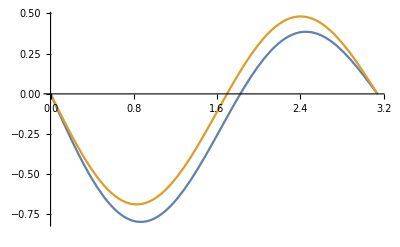

```mathematica
xSignalS0[β_, ξ_, dmJ_] := -Sin[β] Cos[ξ]^2 Sin[ξ]^2 Sin[2 dmJ ]-1/2 Sin[2β] Cos[ξ]^4 Sin[2 dmJ ]
xSignalUdInt[β_, ξ_, dmJ_] :=- Sin[β]  Cos[ξ]^2 Sin[ξ]^2 Sin[2 dmJ ] - Sin[2β] ( Cos[ξ]^4 Sin[2 dmJ ])
dmJ = 1
ξξ = ArcTan[0.5]
Plot[{2*xSignalS0[β, ξξ, dmJ], xSignalUdInt[β, ξξ, dmJ]}, {β, 0, π}]
```

## Final recap

The operators considered here are:
Szz
Sza + Szb
Sza - Szb
Sxx + Syy
Sya - Syb -> 0
Syz + Szy -> 0
Sxa - Sxb -> 0
Sxz + Szx -> 0
Sxx - Syy
Sxy + Syx
Sxx
Syy